1.45455×10^-2

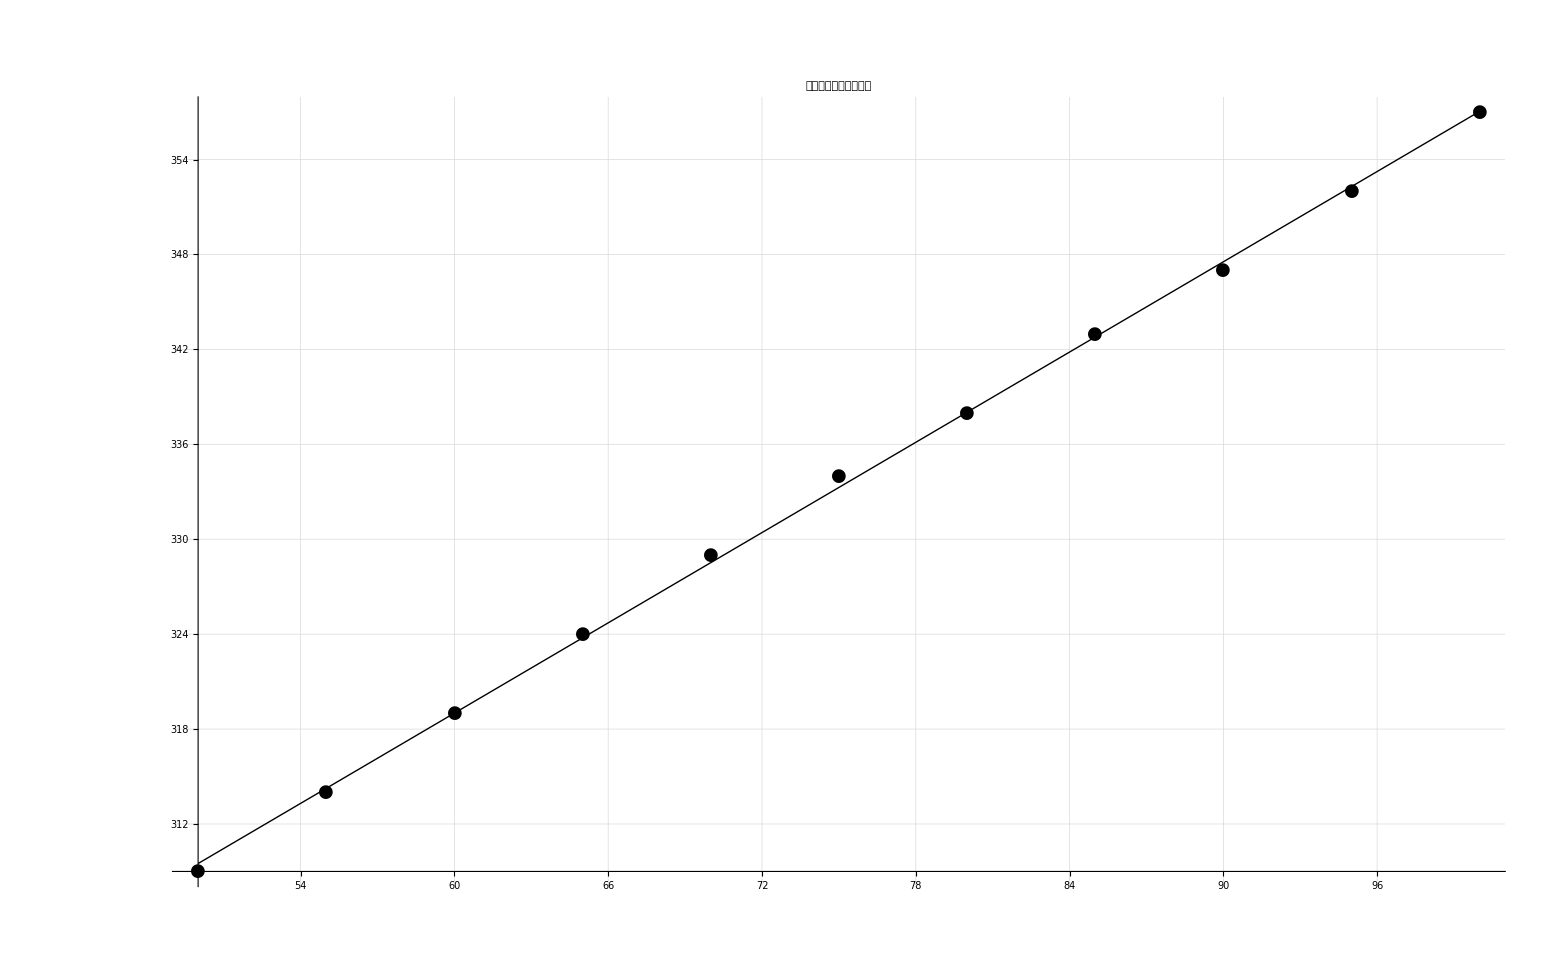

{{50,55,60,65,70,75,80,85,90,95,100},{309,314,319,324,329,334,338,343,347,352,357}}

/Users/timfeirg/Documents/Medical-Sensor-Experiments/Exp10.xlsx

```mathematica
(*exp10*)
temperature=Range[50,100,5];
volts={309,314,319,324,329,334,338,343,347,352,357};
coordinatesExp10=Transpose[{temperature,volts}];
linearFitExp10=LinearModelFit[coordinatesExp10,x,x];
PlotGraph=ListPlot[
coordinatesExp10,
PlotMarkers->{Automatic,18},
PlotStyle->Black,
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dashed],
Frame->Automatic,
FrameLabel->{"T/°C","V/mV"},
PlotLabel->"集成温度传感器的特性",
BaseStyle->{FontWeight->"Bold",FontSize->18}
];
regressionExp10=Plot[Normal[linearFitExp10],
{x,Max[temperature],Min[temperature]},
PlotStyle->{Black,Thick}];
errorExp10=Max[Abs[linearFitExp10["FitResiduals"]]]/(Max[temperature]-Min[temperature])//ScientificForm
Show[PlotGraph,regressionExp10]
fullForm={temperature,volts}
Export["/Users/timfeirg/Documents/Medical-Sensor-Experiments/Exp10.xlsx",fullForm,"XLSX"]
```